```mathematica
BesselI[0,0]
Integrate[Cos[x y],{x,0,1},{y,0,x}]
```

1

SinIntegral[1]/2

```mathematica
-BesselI[0,r]BesselK[0,R]HeavisideTheta[R-r]-BesselI[0,R]BesselK[0,r]HeavisideTheta[r-R]
```

-BesselI[0,R] BesselK[0,r] HeavisideTheta[r-R]-BesselI[0,r] BesselK[0,R] HeavisideTheta[-r+R]

```mathematica
(1.878*10^8)/(5*5^2*10^(-18)*(2*Pi)^(1.5))
```

9.53928×10^22

```mathematica
Cos[X-x](-BesselI[0,R] BesselK[0,r] HeavisideTheta[r-R]-BesselI[0,r] BesselK[0,R] HeavisideTheta[-r+R])((1.878*10^8)/(5*5^2*10^(-18)*(2*Pi)^(1.5)) Exp[-R^2/(2*(5*10^(-6))^2)-x^2/(2*(5*10^(-6))^2)])R
```

9.53928×10^22 ⅇ^(-20000000000 x^2-20000000000 y^2)

```mathematica
kp=1.83*10^5;
e= 1.60217662*10^(-19);
epsilon0:= 8.85*10^(-12);
r=0;
y2[X_]:=-((e *kp^2)/(epsilon0))Integrate[Cos[kp(X-x)](-BesselI[0,kp*R] BesselK[0,kp*r] HeavisideTheta[r-R]-BesselI[0,kp*r] BesselK[0,kp*R] HeavisideTheta[-r+R])((1.878*10^8)/(5*(8.5/3)^2*10^(-18)*(2*Pi)^(1.5)) Exp[-R^2/(2*((8.5/3)*10^(-6))^2)-x^2/(2*(5*10^(-6))^2)])R,{x,-Infinity,X},{R,0,Infinity}]

y[0 *10 ^(-6)]
```

Indeterminate

```mathematica
kp=1.83*10^5;
e= 1.60217662*10^(-19);
epsilon0= 8.85*10^(-12);
r=0;
y[X_]:=-((e *kp^2)/(epsilon0))Integrate[Cos[kp(X-x)](-BesselK[0,kp*R] )((1.878*10^5)/(5*5^2*10^(-18)*(2*Pi)^(1.5)) R*Exp[-R^2/(2*(5*10^(-6))^2)-(x)^2/(2*(5*10^(-6))^2)]),{x,+Infinity,X},{R,0,Infinity}]


y[0 *10^(-6)]
```

-3.04513×10^6

```mathematica
points=Table[{x,y[x]},{x,Range[1*10^(-6),10*10^(-6),5*10^(-6)]}];
```

Integrate::ilim: Invalid integration variable or limit(s) in {1/1000000,-∞,1/1000000}.

Integrate::ilim: Invalid integration variable or limit(s) in {3/500000,-∞,3/500000}.

```mathematica
RealDigits[5.193512495014662*^9]
```

{{5,1,9,3,5,1,2,4,9,5,0,1,4,6,6,2},10}

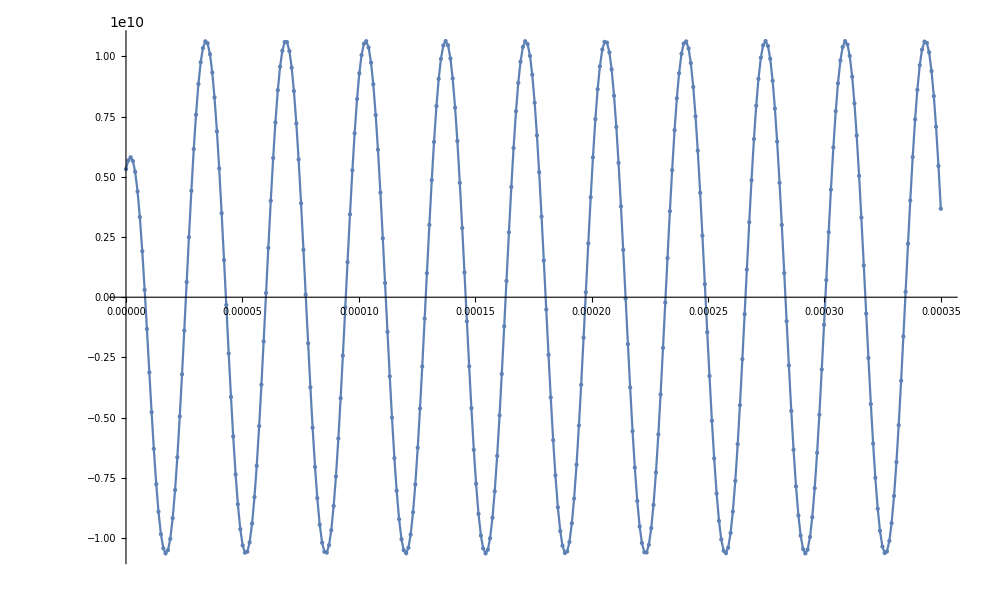

```mathematica
fig=Plot[y[a],{a,0*10 ^(-6),350*10 ^(-6)},Mesh->All,MaxRecursion->0,PlotPoints->350]
```

```mathematica
Do[Print[Re[y[i*10^(-6)]]],{i,-10,9,1}]
```

$Aborted

```mathematica
(1*10^4)/(50*10^2*10^(-18)*(2*Pi)^(1.5))
```

1.26987×10^17